### Problem 1

```mathematica
(*Are the eigenstates orthonormal?*)
$Assumptions=Element[n,Integers]&&Element[m2,Integers];ψeigen[x_,n_]:=√(2/a)Sin[(n π x)/a]
Integrate[ψeigen[x,n]ψeigen[x,m2],{x,0,a}]
Integrate[ψeigen[x,n]ψeigen[x,n],{x,0,a}]
(*They are orthonormal*)
```

0

1

### Problem 2

ψ = √(2/a)(sin((2 πx)/a) + 2 sin(πx/a))/(√5)
Is the wave function normalized?
	When we square and integrate, after all of the 1’s and 0’s disappear, we get (1+4)/5=1, so it is normalized.
What is the expectation value of energy?
	(hbar^2 π^2)/(5m a^2)+(2 hbar^2 π^2)/(5m a^2)=(3 hbar^2 π^2)/(5m a^2)
What is the probability that E_(1,)E_(2,)and E_3 will be measured?
	P(E_1) = 4/5
	P(E_2) = 1/5
	P(E_3) = 0

### Problem 3

```mathematica
ψ=(√2)/2;
(*Is the wave function normalized?*)
a=5;
Integrate[ψ^2,{x,a/2-1,a/2+1}]
```

1

```mathematica
(*What is Subscript[c, n]?*)
c[n_]=Integrate[ψ √(2/a)Sin[(n π x)/a],{x,a/2-1,a/2+1}]
```

(√5 (Cos[(3 n π)/10]-Cos[(7 n π)/10]))/(n π)

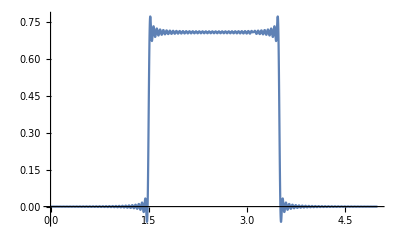

```mathematica
(*Does the wave look correct?*)
Plot[Sum[c[n] √(2/a)Sin[(n π x)/a],{n,200}],{x,0,a}]
```

```mathematica
(*What is <E>?*)
Sum[Integrate[(n^2 hbar^2 π^2)/(2m a^2)c[n]^2 2/a Sin[(n π x)/a]^2,{x,0,a}],{n,20}]//Simplify
```

(2 hbar^2)/m

```mathematica
(*What are the probabilities of the energy occuring?*)
c[1]^2//N
c[2]^2//N
c[3]^2//N
c[4]^2//N
```

0.700112

0.

0.203657

0.

```mathematica
(*Create an animation of the wave function (I did ψψ^*)*)
hbar=1;
m=1;
En=(n^2 hbar^2 π^2)/(2m a^2);
Animate[Plot[Re[Sum[c[n] √(2/a)Sin[n π x/a] ⅇ^(-ⅈ En t/hbar),{n,20}]]^2+Im[Sum[c[n] √(2/a)Sin[n π x/a] ⅇ^(-ⅈ En t/hbar),{n,20}]]^2,{x,0,a}],{t,0,1},AnimationRunning->False]
```